# std::Math An implementation of standard math functions in Rust, rather than importing from a C library.

## pow(mantissa: float, exponent: float)

```mathematica
Normal[Series[
```

## sin(angle: float)

theta-theta^3/6+theta^5/120-theta^7/5040+theta^9/362880-theta^11/39916800+theta^13/6227020800-theta^15/1307674368000+theta^17/355687428096000-theta^19/121645100408832000

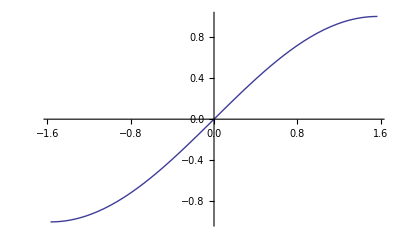

2.3743×10^-16

```mathematica
clear[f,theta,g];
sinApprox[theta_] = Normal[Series[Sin[theta],{theta,0,20}]]
Plot[sinApprox[theta],{theta, -Pi/2,Pi/2}]
N[Abs[Sin[Pi/2]-sinApprox[Pi/2]]]
```